# Learning Reliability

We can use this plot to discover various distributions similar to the reliability.

```mathematica
Show[WolframLanguageData["ReliabilityDistribution","RelationshipCommunityGraph"],ImageSize->800]
```

-Graphics-

We can take the reliability distribution given the lifetime of X and Y.

```mathematica
?ReliabilityDistribution
```

```mathematica
R=ReliabilityDistribution[x∧y,{{x,ExponentialDistribution[Subscript[l,1]]},{y,ExponentialDistribution[Subscript[l,2]]}}]
```

ReliabilityDistribution[x1&&x2,{{x1,ExponentialDistribution[l_1]},{x2,ExponentialDistribution[l_2]}}]

The mean of the reliability distribution is 1/(Sum of lifetimes).

```mathematica
Mean[R]
```

1/(l_1+l_2)

What if it is X or Y? This means X and Y are redundancies?

```mathematica
R=ReliabilityDistribution[x∨y,{{x,ExponentialDistribution[Subscript[l,1]]},{y,ExponentialDistribution[Subscript[l,2]]}}];
```

We can ask the following.
What is the mean of a reliability distribution x or y?
Can we assume both x and y are distributed with the exponential distribution?

```mathematica
Mean[R]
```

1/l_1+1/l_2-1/(l_1+l_2)

```mathematica
R=ReliabilityDistribution[x∧(y∨z),{{x,ExponentialDistribution[3]},{y,ExponentialDistribution[1]},{z,ExponentialDistribution[2]}}];
```

Time from 0 to 2

```mathematica
?SurvivalFunction
```

```mathematica
?HazardFunction
```

```mathematica
?PDF
```

```mathematica
?CDF
```

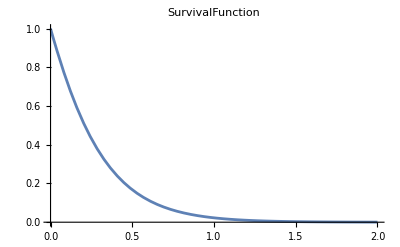
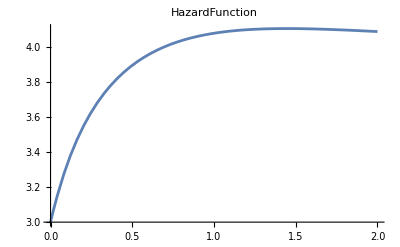
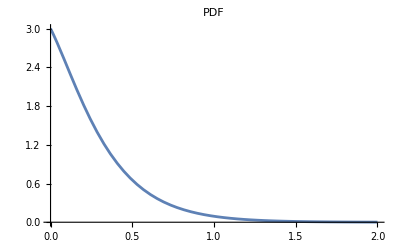
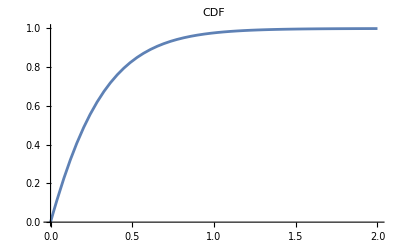

```mathematica
Table[Plot[df[R,t],{t,0,2},PlotLabel->df,PlotRange->All],{df,{SurvivalFunction,HazardFunction,PDF,CDF}}]
```

```mathematica
{Mean[R],Median[R]}
```

{17/60,Log[Root[2-2 #1-2 #1^2+#1^6&,2,0]]}

What does the mean and median of R represent?

```mathematica
{Mean[R],Median[R]};
N[%]
```

{0.283333,0.208872}

This answers the question, what is the probability of failure of the time being less than half.
Suppose the time follows a reliability distribution R as defined above.

```mathematica
Probability[t<0.5,t\[Distributed]R]
```

0.832367